```mathematica
lst=Table[0,8,61];
For[gg=0,gg<8,gg++,{seigenVa,seigenVeL,seigenVeR,snessDist,sxExp,syExp}={eigenVa,eigenVeL,eigenVeR,nessDist,xExp,yExp}/.{g->gg,h->10};
nseigenVeL=Table[seigenVeL[[i]]/(seigenVeL[[i]].seigenVeR[[i]]),{i,1,8}];lst[[gg+1]]=Table[fCtauN[i],{i,-30,0}]~Join~Table[fCtauP[i],{i,1,30}]];
General::munfl: "\!\(\*RowBox[{\"Exp\", \"[\", RowBox[{\"-\", \"733.4204841489715`\"}], \"]\"}]\) is too small to represent as a normalized machine number; precision may be lost."
General::munfl: "\!\(\*RowBox[{\"Exp\", \"[\", RowBox[{\"-\", \"1463.1378463776634`\"}], \"]\"}]\) is too small to represent as a normalized machine number; precision may be lost."
General::munfl: "\!\(\*RowBox[{\"Exp\", \"[\", RowBox[{\"-\", \"708.973134677339`\"}], \"]\"}]\) is too small to represent as a normalized machine number; precision may be lost."
General::stop: "Further output of \!\(\*StyleBox[RowBox[{\"General\", \"::\", \"munfl\"}], \"MessageName\"]\) will be suppressed during this calculation."
```

```mathematica
Rasterize[ListPlot[lst,PlotLegends->Table[i,{i,0,7}],DataRange->{-30,30},Joined->True]]
```

-Graphics-

```mathematica
Export["F:\\ThesisProject\\RESULTS\\22052023_corr_ana_h10\\corr_ana.dat",lst]
corr0=ReadList["F:\\ThesisProject\\RESULTS\\22052023_corr_ana_h10\\corr_s_0.dat",Number];
corr1=ReadList["F:\\ThesisProject\\RESULTS\\22052023_corr_ana_h10\\corr_s_1.dat",Number];
corr2=ReadList["F:\\ThesisProject\\RESULTS\\22052023_corr_ana_h10\\corr_s_2.dat",Number];
corr3=ReadList["F:\\ThesisProject\\RESULTS\\22052023_corr_ana_h10\\corr_s_3.dat",Number];
corr4=ReadList["F:\\ThesisProject\\RESULTS\\22052023_corr_ana_h10\\corr_s_4.dat",Number];
corr5=ReadList["F:\\ThesisProject\\RESULTS\\22052023_corr_ana_h10\\corr_s_5.dat",Number];
corr6=ReadList["F:\\ThesisProject\\RESULTS\\22052023_corr_ana_h10\\corr_s_6.dat",Number];
corr7=ReadList["F:\\ThesisProject\\RESULTS\\22052023_corr_ana_h10\\corr_s_7.dat",Number];
```

F:\ThesisProject\RESULTS\22052023_corr_ana_h10\corr_ana.dat

```mathematica
plst=Table[0,{i,8},{j,31},{k,2}];
For[i=0,i<8,i++,plst[[i+1]]=Transpose[{Table[i,{i,-30,30}],lst[[i+1]]}]];
```

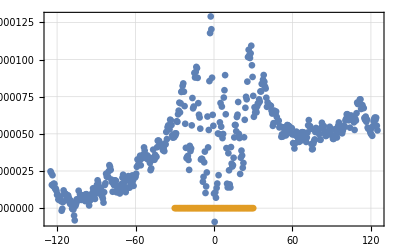

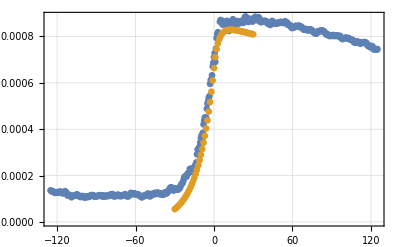

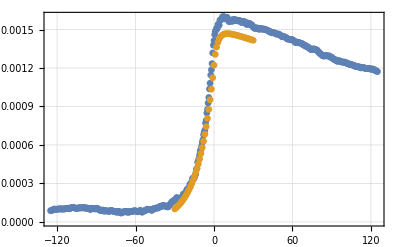

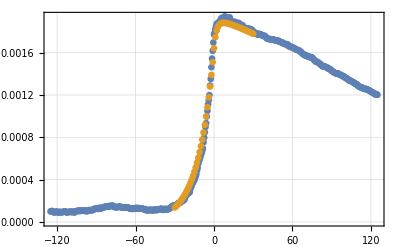

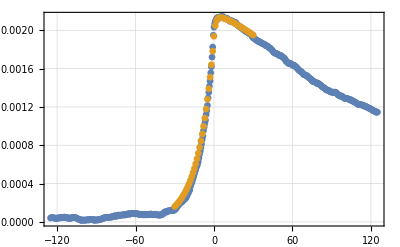

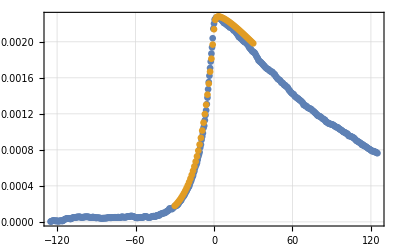

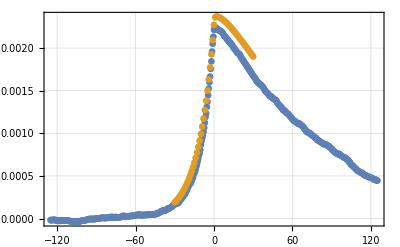

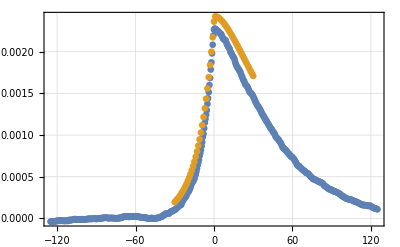

```mathematica
scalF=10;
pcr0=Transpose[{Table[i,{i,-12.5*scalF,12.5*scalF,0.05*scalF}],corr0}];

ListPlot[{pcr0,plst[[1]]},PlotStyle->PointSize[0.012],PlotTheme->"Detailed",PlotRange->All,DataRange->{-30.30}]
pcr1=Transpose[{Table[i,{i,-12.5*scalF,12.5*scalF,0.05*scalF}],corr1}];

ListPlot[{pcr1,plst[[2]]},PlotStyle->PointSize[0.012],PlotTheme->"Detailed",PlotRange->All,DataRange->{-30.30}]
pcr2=Transpose[{Table[i,{i,-12.5*scalF,12.5*scalF,0.05*scalF}],corr2}];

ListPlot[{pcr2,plst[[3]]},PlotStyle->PointSize[0.012],PlotTheme->"Detailed",PlotRange->All,DataRange->{-30.30}]
pcr3=Transpose[{Table[i,{i,-12.5*scalF,12.5*scalF,0.05*scalF}],corr3}];

ListPlot[{pcr3,plst[[4]]},PlotStyle->PointSize[0.012],PlotTheme->"Detailed",PlotRange->All,DataRange->{-30.30}]
pcr4=Transpose[{Table[i,{i,-12.5*scalF,12.5*scalF,0.05*scalF}],corr4}];

ListPlot[{pcr4,plst[[5]]},PlotStyle->PointSize[0.012],PlotTheme->"Detailed",PlotRange->All,DataRange->{-30.30}]
pcr5=Transpose[{Table[i,{i,-12.5*scalF,12.5*scalF,0.05*scalF}],corr5}];

ListPlot[{pcr5,plst[[6]]},PlotStyle->PointSize[0.012],PlotTheme->"Detailed",PlotRange->All,DataRange->{-30.30}]
pcr6=Transpose[{Table[i,{i,-12.5*scalF,12.5*scalF,0.05*scalF}],corr6}];

ListPlot[{pcr6,plst[[7]]},PlotStyle->PointSize[0.012],PlotTheme->"Detailed",PlotRange->All,DataRange->{-30.30}]
pcr7=Transpose[{Table[i,{i,-12.5*scalF,12.5*scalF,0.05*scalF}],corr7}];

ListPlot[{pcr7,plst[[8]]},PlotStyle->PointSize[0.012],PlotTheme->"Detailed",PlotRange->All,DataRange->{-30.30}]
```

```mathematica
(**)
```

```mathematica
lst=Table[0,8,31];
For[gg=0,gg<8,gg++,{seigenVa,seigenVeL,seigenVeR,snessDist,sxExp,syExp}={eigenVa,eigenVeL,eigenVeR,nessDist,xExp,yExp}/.{g->gg,h->7};
nseigenVeL=Table[seigenVeL[[i]]/(seigenVeL[[i]].seigenVeR[[i]]),{i,1,8}];lst[[gg+1]]=Table[fDCtau[i],{i,0,30}]];
```

General::munfl: 8.59599×10^-302 1.48915×10^-16 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-712.565] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-737.136] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
Rasterize[ListPlot[lst,PlotLegends->Table[i,{i,0,7}],DataRange->{0,30},Joined->True]]
```

-Graphics-

```mathematica
(*24.05.2023*)
```

```mathematica
max1=ImportString[Import["F:\\ThesisProject\\RESULTS\\24052023_extrema\\h1.txt"],"Data"];
max4=ImportString[Import["F:\\ThesisProject\\RESULTS\\24052023_extrema\\h4.txt"],"Data"];
max7=ImportString[Import["F:\\ThesisProject\\RESULTS\\24052023_extrema\\h7.txt"],"Data"];
max10=ImportString[Import["F:\\ThesisProject\\RESULTS\\24052023_extrema\\h10.txt"],"Data"];
max13=ImportString[Import["F:\\ThesisProject\\RESULTS\\24052023_extrema\\h13.txt"],"Data"]
```

{{4.769756589695362*^-9,1.6282089083761684*^-27},{0.000332398,28.5502},{0.000481201,13.9992},{0.000533496,5.81894},{0.000552089,2.24996},{0.000558832,0.843757}}

```mathematica
maxc={max1[[All,1]],max4[[All,1]],max7[[All,1]],max10[[All,1]],max13[[All,1]]};
maxc[[All,1]]=Table[0,5];
maxc//MatrixForm
```

(0 | 0.0562453 | 0.0887259 | 0.102058 | 0.107213 | 0.10916
0 | 0.0233935 | 0.0353066 | 0.0400117 | 0.0418152 | 0.0424933
0 | 0.00625079 | 0.0091827 | 0.0102691 | 0.0106702 | 0.0108184
0 | 0.0014678 | 0.00213307 | 0.0023707 | 0.00245623 | 0.00248632
0 | 0.000332398 | 0.000481201 | 0.000533496 | 0.000552089 | 0.000558832)

```mathematica
maxt={max1[[All,2]],max4[[All,2]],max7[[All,2]],max10[[All,2]],max13[[All,2]]};
maxt[[All,1]]=Table[0,5];
maxt//MatrixForm
```

(0 | 0.269867 | 0.129315 | 0.052779 | 0.0202246 | 0.00755684
0 | 0.964786 | 0.476559 | 0.200015 | 0.0778965 | 0.0293205
0 | 3.3005 | 1.62697 | 0.679211 | 0.26338 | 0.0989795
0 | 10.101 | 4.96469 | 2.0674 | 0.800207 | 0.301444
0 | 28.5502 | 13.9992 | 5.81894 | 2.24996 | 0.843757)

```mathematica
Rasterize[ListPlot[maxc,PlotLegends->Table[i,{i,1,13,3}],DataRange->{0,10},Joined->True]]
```

-Graphics-

```mathematica
Rasterize[ListPlot[maxt,PlotLegends->Table[i,{i,1,13,3}],DataRange->{0,10},PlotRange->All,Joined->True]]
```

-Graphics-

```mathematica
(*25.05.2023*)
Export["F:\\ThesisProject\\RESULTS\\25052023_extrema\\h10.dat",lst]
```

F:\ThesisProject\RESULTS\25052023_extrema\h10.dat

```mathematica
ilst=Import["F:\\ThesisProject\\RESULTS\\25052023_extrema\\h10.dat","Table"];
```

```mathematica
ilst[[1]]={0,Infinity};
```

```mathematica
fitMax=Transpose[{Table[i,{i,0,12,0.5}],ilst[[All,1]]}];
fitTMax=Transpose[{Table[i,{i,0,12,0.5}],ilst[[All,2]]}];
```

FittedModel[-0.0000219197+0.00102339 x-0.00016372 x^2+0.0000119369 x^3-3.28706×10^-7 x^4]

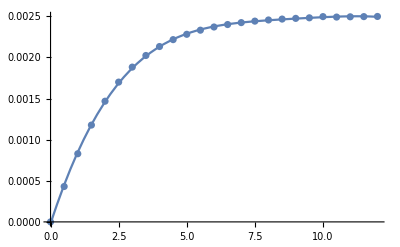

```mathematica
nlm=NonlinearModelFit[fitMax,a+b x+c x^2+d x^3+e x^4,{a,b,c,d,e},x]
Show[ListPlot[ilst[[All,1]],DataRange->{0,12},PlotRange->All],Plot[nlm[x],{x,0,12}]]
```

FittedModel[18.7195-1.50103/x-4.71804 x+0.371601 x^2-0.00456264 x^3-0.000364738 x^4]

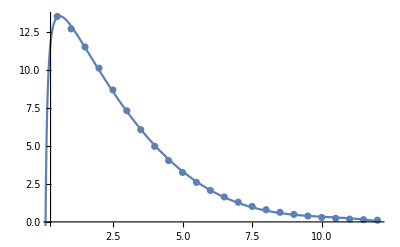

```mathematica
nlmt=NonlinearModelFit[fitTMax[[2;;25]],a+b x+c x^2+d x^3+e x^4+f x^(-1),{a,b,c,d,e,f},x]
Show[ListPlot[ilst[[All,2]],DataRange->{0,12},PlotRange->All],Plot[nlmt[x],{x,0,12}]]
```

```mathematica
Export["F:\\ThesisProject\\RESULTS\\25052023_extrema\\fit.dat",{nlm//Normal,nlmt//Normal}]
```

F:\ThesisProject\RESULTS\25052023_extrema\fit.dat